## Walker — Oscillations and Waves Exam 2

## April 4, 2025

## Longitudinal Waves in Two Dimensions

## The Physics Problem: We are going to set off an explosion in the middle of a two-dimensional grid of masses. The explosion could be most anything, including a bullet entering a material, which behaves much like an explosion within the surface. The explosion will create a radially outward set of initial velocities, which will turn into radially outward displacements. The wave will also travel radially outward. Because we have radial displacement and radial wave motion, this notebook complements the previous notebook by illustrating longitudinal waves, also called “compression” waves. A surprising thing is that at the center of the blast, the explosion outward is followed by movement inward, and this simulation will show that. For multiple reasons, I am dropping back to two dimensions int this notebook (after we explored three dimensions in the last notebook): (1) Three-dimensional simulations are taxing the heck out of some people’s laptops. (2) Three-dimensional simulations are harder to visualize simply due to the sheer crowding of the graphics. (3) It will be faster in an exam situation to only have to deal with code in two dimensions. (4) Most of the intuition you can build in three dimensions can be built in two or even one dimension. This is especially true of compression waves.

## Directions: After downloading this notebook, rename it with your first name in the filename. E.g., Eli-Exam2.nb, Harper-Exam2.nb, Hexi-Exam2.nb, Jeremy-Exam2.nb, Rania-Exam2.nb, Tahm-Exam2.nb, or Walker-Exam2.nb. Then disconnect from the wifi and work the exam. Save your notebook early and often so that you don’t lose work in progress. When you are done, save your notebook one last time, re-join the wifi, and then email it to me.

### Initial Conditions for the Simulation

Set up the duration, steps, and deltaT:

```mathematica
tInitial = 0.0;
tFinal = 10.0;
steps = 2400;
deltaT = (tFinal - tInitial)/steps;
```

Set up the size of the grid (enough masses so that the grid is recognizably starting to form a continuum, but not so many that we tax our computers). During debugging of the code, we will keep the number of masses very small:

### Initial Velocities for the Simulation

Below is some code that you will partially recognize from my mallet strike code, although it isn’t identical. The initial position are all zero. The explosion creates radial initial velocities. It is 100% working already, so don’t mess with it unless you have a lot of spare time and are curious.

```mathematica
nx=41;  (* An odd number so the center will be an integer. *)
ny=31; (* Again, an odd number so the center will be an integer. *)
initialXArray=Table[0,nx,ny];
initialYArray = Table[0,nx,ny];
explosionCenterX=(nx+1)/2;
explosionCenterY=(ny+1)/2;
explosionMagnitude = 10;
explosionBreadth=5;
initialVxArray=Array[
explosionMagnitude(#1-explosionCenterX)/explosionBreadth^2 Exp[-((#1-explosionCenterX)^2+(#2-explosionCenterY)^2)/explosionBreadth^2]&,
{nx,ny}
];
initialVyArray=Array[
explosionMagnitude(#2-explosionCenterY)/explosionBreadth^2 Exp[-((#1-explosionCenterX)^2+(#2-explosionCenterY)^2)/explosionBreadth^2]&,
{nx,ny}
];
initialConditions={tInitial,initialXArray,initialVxArray,initialYArray,initialVyArray};
```

### 1. Building the Graphics and Displaying the Initial Velocities (6 pts)

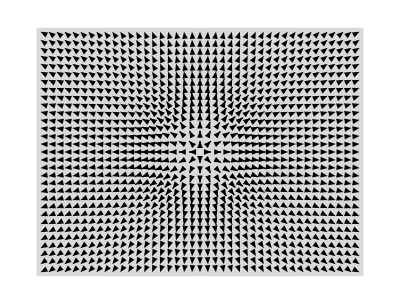

```mathematica
width=nx+1;
depth=ny+1;
xspacing=width/nx; 
yspacing=depth/ny; 
rectangle=Style[Rectangle[{-width/2,-depth/2},{width/2,depth/2}],LightGray];
pointRestPosition[j_,k_]:={-width/2+(j-1/2) xspacing,-depth/2+(k-1/2) yspacing}
pointDisplacedPosition[j_,k_,xs_,ys_]:=pointRestPosition[j,k]+{xs[[j,k]],ys[[j,k]]}
arrayGraphic[xs_,ys_]:=Graphics[Flatten[{

{rectangle},
{Arrowheads[0.02]},
Table[Arrow[{pointRestPosition[j,k],pointDisplacedPosition[j,k,xs,ys]}],{j,nx},{k,ny}]

(* QUARKS AND ANTIQUARKS *)

(* Look up the documentation for Arrow. You need a table that puts in *)
(* all the arrows. The tails of the arrows go at pointRestPosition[]. *)
(* The heads of the arrows go at pointDisplacedPosition[]. *)
},1]];
arrayGraphic[initialConditions[[3]],initialConditions[[5]]]
```

The array graphic can be used to display the velocities, or it can be used to display the displacements. Just below, to test your arrayGraphic[] code, I have taken a screenshot of my graphics being used to display the velocities. If your graphics don’t display velocities similarly to my screenshot below, keep debugging.

-Graphics-

### Formulas for the Accelerations — Theory

We have two directions in which the masses can move. Not surprisingly, we now have two acceleration formula:

a_x_(j,k)=v_0^2(x_(j+1,k)+x_(j-1,k)+x_(j,k+1)+x_(j,k-1)-4 x_(j,k))

a_y_(j,k)=v_0^2(y_(j+1,k)+y_(j-1,k)+y_(j,k+1)+y_(j,k-1)-4 y_(j,k))

#### Periodic Boundary Conditions

Because it is kind of simple and it is what we did in the last notebook, we will again use periodic boundary conditions. However, for a problem involving an explosion at a single location, it is an unphysical choice. It is as if we have set off an infinite number of equally-spaced explosions throughout the universe. We’ll keep the simulation duration short so that we don’t see much of the resulting chaos arriving at our little patch of the universe.

### 2. Implementing the Accelerations (6 pts)

```mathematica
v0=Pi/3; 

(* CHARGED AND NEUTRAL LEPTONS *)

(* I did one term of one of the x accelerations. You have four more terms and then all the *)
(* y acceleration terms to code up using the formulas above. *)
(* You may of course consult the notebook *)
(* we finished in the last class. *)

ax[j_,k_,allxs_]:= v0^2(If[j==nx,allxs[[1,k]],allxs[[j+1,k]]]+
If[j==1,allxs[[nx,k]],allxs[[j-1,k]]]+
If[k==ny,allxs[[j,1]],allxs[[j,k+1]]]+
If[k==1,allxs[[j,ny]],allxs[[j,k-1]]]-
4allxs[[j,k]])

ay[j_,k_,allys_]:= v0^2(If[j==nx,allys[[1,k]],allys[[j+1,k]]]+
If[j==1,allys[[nx,k]],allys[[j-1,k]]]+
If[k==ny,allys[[j,1]],allys[[j,k+1]]]+
If[k==1,allys[[j,ny]],allys[[j,k-1]]]-
4allys[[j,k]])
```

### 3. Second-Order Runge-Kutta — Implementation (8 pts)

```mathematica
rungeKutta2[cc_]:= (
curTime=cc[[1]];
curXArray=cc[[2]];
curVxArray=cc[[3]];
curYArray=cc[[4]];
curVyArray=cc[[5]];
newTime=curTime+deltaT;
xStarArray=curXArray+curVxArray deltaT/2;
yStarArray=curYArray+curVyArray deltaT/2;
xAccelerations=Table[ax[j,k,xStarArray],{j,1,nx},{k,1,ny}];
yAccelerations=Table[ay[j,k,yStarArray],{j,1,nx},{k,1,ny}];
newVxArray=curVxArray+xAccelerations deltaT;
newVyArray=curVyArray+yAccelerations deltaT;
newXArray=curXArray+(curVxArray+newVxArray)deltaT/2;
newYArray=curYArray+(curVyArray+newVyArray)deltaT/2;


(* VECTOR BOSONS AND THE HIGGS *)

(* I left all of the Runge-Kutta2 work for you!! EGADZ!! This is definitely the *)
(* part of the exam that is going to require the most work. *)

(* HINT: What do we always do and how does it apply here? In Runge-Kutta 2, *)
(* we first compute an xStarArray and a yStarArray. Then we compute *)
(* the midpoint xAccelerations and the yAccelerations. *)
(* Then we compute newVxArray and newVyArray. Finally we compute *)
(* newXArray and newYArray using the trapezoid approximation. *) 
(* Consult the previous notebook if this hint isn't helping you! However, *)
(* it isn't just a copy-and-paste job. We now have motion in the x and y *)
(* directions. In the previous notebook we only had motion in one *)
(* direction (the z direction). This notebook can actually do both *)
(* longitudinal and transverse waves with the right initial conditions. :) *)

(* When you are done, the things you just calculated are returned as a list: *)
{newTime,newXArray,newVxArray, newYArray,newVyArray}
)

rk2ResultsTransposed=Transpose[NestList[rungeKutta2,initialConditions, steps]];
xResults=rk2ResultsTransposed[[2]];
yResults=rk2ResultsTransposed[[4]];
```

### Animation

Animation is really taxing on people’s computers while they are trying to get debugging done, so I am only putting a screenshot in here.

Once you have your debugging done, put in the code in my screenshot and play your animation. If your animation doesn’t look like mine when the animation is about 85% done as shown below, keep debugging!

```mathematica
Animate[arrayGraphic[xResults[[step]],yResults[[step]]],{step,0,steps,1},DefaultDuration->tFinal-tInitial]
```

-Graphics-

### Comment

This is all supposed to be a fun and whirlwind introduction to complex physics. Notice that in the plot above, at the center of the explosion, the arrows have turned around! Does that make any sense? Does it exist in the real world? Well, yes it does, and here are two examples. (1) Drop coming back out of the center (https://www.smithsonianmag.com/smart-news/researchers-figure-out-why-water-droplets-go-plink-180969440/):

-Graphics-

(2) Lunar impact crater with rock coming back up in the center and forming a central peak:

-Graphics-

“Central peaks are thought to result from the convergence of inward-collapsing material temporarily forced outward by the impactor, combined with localized unloading of the deeper horizons of the impacted material.” https://princegeology.com/central-peak-formation-in-model-impact-craters/